# Monte Carlo Methods for Stochastic Differential Equations

## ACM40730 Mathematica for Research Project Uche Mbaka : 19201613

## Introduction

Solving stochastic differential equations numerically can be viewed as a type of Monte Carlo simulation. Given a Stochastic differential equation, we can approximate the final expected value of the solution E[X_t], using Monte-Carlo and some discretization method.

E[x_t] = 1/n∑_(s=1)^n X_F^(s)

where X_F^(s)denote the final time approximation of the s^th path using some discretization method. 
In this report we will explore ways of estimating E[X_t ] and E[f(X_t)], using functions and combination of functions in Mathematica. For Expected values of some function of X_t, (E[f(X_t)]) will consider the example of European option pricing , using the Black -Scholes Model and the Heston model .There  are various discretization methods, only two of which will  be discussed in this report the Euler-Maruyama and the Milstein discretization scheme.
The estimated call price will be compared with the exact price for the Black Scholes model. 

This report will showcase most of the topics learnt in Mathematica for Research module. This will lead to unnecessary use of some functions.

### Stochastic Differential Equation

An ordinary differential equation (ODE) can be used to describe a deterministic process, example

(dX(t))/dt = f(X,t)
or 
dX(t) = f(X,t)dt

f(X,t) is deterministic with X(0) = X_0. Equation 1 can be written in integral form in the time interval [0,t]

X(t) = X(0)+(∫_0)^t f(X(s),s)ⅆs

Example of equation 1;

dX(t) = X^2(t) - 3 dt
written in the form of equation 2
X = ∫(t^2 - 3)ⅆt

```mathematica
DSolve[y'[x] == 5 x^2-3, y[x],x]
```

{{y[x]→-3 x+(5 x^3)/3+C[1]}}

X(t) is a deterministic process and future values can be predicted .
Lets consider a model that includes some random phenomena (most real life problem), it will no longer be a deterministic process and future values cannot be predicted, example

(dX(t))/dt= a(t)X(t)
X(0) = X_0 and a is a non deterministic term that can be expressed in the form 
a(t) = μ(t) + h(t)σ(t)

hence, we have

(dX(t))/dt = μ(t)X(t) + h(t)σ(t)X(t)

with dW(t) = h(t) representing a differential form of the Wiener process. Equation 4 can then be written as

dX(t) = μ(t)X(t)dt+σ(t)X(t)dW(t)
or
dX_t = μ(X_t)dt + σ(X_t)dW_t

Equation 5 is a 1-dimensional stochastic differential equation, where X_t is a stochastic process, μ is the drift coefficient, σ is the diffusion coefficient and W(t)  is the Wiener process. From now on we would use the second form of equation 5.
The first term with drift coefficient μ is non stochastic (deterministic) while the second term with diffusion coefficient σ is stochastic . X_t is a stochastic process that follows the Geometric Brownian motion and the equation can be written in integral form as

X_t = X_0 +(∫_0)^t μ(X_s)ds+(∫_0)^t σ(X_s)dW_s

### Monte Carlo Methods

Monte Carlo methods are numerical methods, where random numbers are used to give an estimate. An example is estimation of an integral. given a simple integral ;

E[X] = (∫_0)^1 f(x)dx

The above integral can be approximated numerically using Monte Carlo method as

E[X] ≈ E[f(U)] = 1/n∑f(u_i)

where U is a uniform random number in [0,1]. Lets take f(x) = x^2, the exact solution using integral is

```mathematica
∫_0^1 x^2 ⅆx
```

1/3

The Monte Carlo estimate, using n = 10000 is

```mathematica
Clear[n];
n = 10000
1/n∑_(i=1)^n RandomVariate[UniformDistribution[{0,1}]]^2
```

0.337396

We see that the exact solution is close to the Monte Carlo estimate. Increasing n would also reduce the difference.The idea of Monte Carlo estimation is very plain and easy to implement. The shortcomings of applying Monte Carlo methods and ways of remedying some of them won’t be discussed in this report.
W_t in equation 5 follows a standard normal distribution (N(0,1)), there are several ways to simulate random variables from such distribution as an example we would consider simulating from a double exponential which will be simulated from a uniform distribution. Assumption:  This example assumes we can only draw samples from uniform distribution.

#### Steps

Use method of inversion and simulate exponential distribution f(x) = λ exp(-λx)

Simulate standard normal using rejection sampling and standard double exponential (Laplace distribution) as envelop function

For step 1
The density function for exponential is given as

f_λ(x) = λ ⅇ^(-λx)

The cumulative distribution function is given as

F_λ(x) = 1-ⅇ^(-λx)

Method of inversion: if we solve for x in the  equation above the CDF of exponential we get the inverse .

x = F^-1= (-log(1-U))/λ

we generate 100 exponential random variate x ~ exp(1): λ = 1

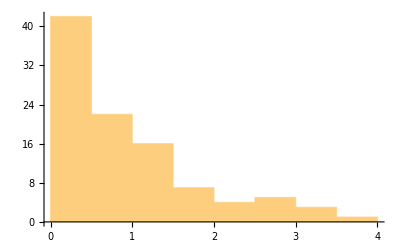

```mathematica
Clear[X];
X = Table[(-Log[1-RandomVariate[UniformDistribution[{0,1}]]])/λ, {i,1 , 100}];
y = X/. λ-> 1;
Histogram[y]
```

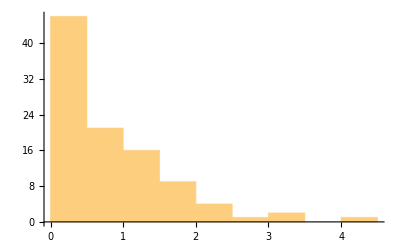

```mathematica
Histogram[Table[RandomVariate[ExponentialDistribution[1]], {i, 1, 100}]](*Default Exponential Distribution Function*)
```

To sample from a standard normal distribution,we using rejection method. Without going into much details of how rejection sampling work. Basically we enclose the proposed density function with a rectangular box and generate points uniformly at random over this region any points outside the density function is rejected and any points underneath are accepted. To overcome some of the shortcomings of this method, the rectangle is replaced with more general curve (some similar distribution) and maximized to reduce rejection probability.

Target distribution f(x) = 1/(√(2π))ⅇ^(-x^2/2)
Envelope distribution h(x) = ⅇ^(-|x|)/2
weighted function w(x) = (f(x))/(h(x)) = (1/(√(2π))ⅇ^(-x^2/2))/(ⅇ^(-|x|)/2)

We won’t border about the absolute value in our envelope distribution

```mathematica
Clear[wx,x];
wx = (1/(√(2π))ⅇ^(-x^2/2))/(ⅇ^-x/2);
```

To minimize the probability of rejection , we bound the w(x) by the constant M > 0 (ideally M should be close to 1). we get g(x) = Mh(x). M ≥ Sup_x {(f(x))/(g(x))}

M = Max(w(x)) = w`(x) = 0

```mathematica
M = Maximize[wx, x]
```

{√((2 ⅇ)/π),{x→1}}

(f(x))/(Mh(x))=(f(x))/(g(x)) = (1/(√(2π))ⅇ^(-x^2/2))/(√((2 ⅇ)/π) ⅇ^-x/2)

```mathematica
(1/(√(2π))ⅇ^(-x^2/2))/(√((2 ⅇ)/π) ⅇ^-x/2)
```

ⅇ^(-1/2+x-x^2/2)

Therefore to generate X ~ N(0,1) as follow

Generate Y ~ Exp(1) as we did above

Generate U ~ U(0,1)

If U ≤ ⅇ^(-1/2+y-y^2/2), set |X| = Y; else go back to 1

Generate U ~ U(0,1), set X = |X| if U ≤ 0.5, else set X = -|X|

```mathematica
stdNormal[n_] :=  Module[{X, y, u, u2},
						X = Range[1,n];
						For[i = 1, i ≤ n, i++,
							While[True,
								y = (-Log[1-RandomVariate[UniformDistribution[{0,1}]]])/1;(*exp(1)*)
								u = RandomVariate[UniformDistribution[{0,1}]];
								If[u ≤ (ⅇ^(-1/2+y-y^2/2)),
									u2 = RandomVariate[UniformDistribution[{0,1}]];(*sign y*)
									If[u2 ≤  0.5, X[[i]] = y; Break[],  X[[i]] = -y;Break[]]]]];
						Return[X]
				];
```

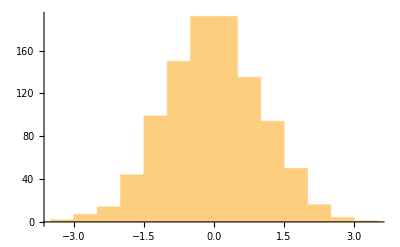

```mathematica
Histogram[stdNormal[1000]]
```

There are different ways of simulating a Normal distribution and the above example is one of such ways. There is a default Normal Distribution function and a Wiener Process in Mathematica and those would be used  as they would be optimized for performance. Also the approach used for writing the function above was a general programming approach and won’t be the best approach using Mathematica. Optimized function are available in Mathematica (e.g Table) that would increase the performance of the function above.

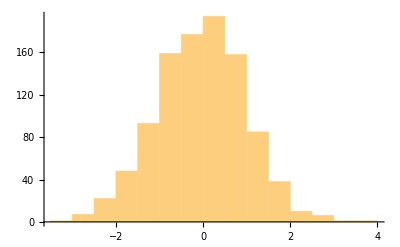

```mathematica
Histogram[Table[RandomVariate[NormalDistribution[0,1]], {i, 1, 1000}]](*Default Nprmal Distribution with mean 0 and var 1Function*)
```

## Stochastic Differential Equations and Monte Carlo Simulation

For this report we will consider simulation in context of option pricing. Our interest will be to generate stock price and estimate interest rate at time t. Typically stock prices and interest rates are assumed to be driven by a continuous time stochastic process. Simulation however, is done at discrete time steps. For discretization, we will as earlier stated discuss the Euler-Maruyama scheme and Milstein scheme and will apply both to Black-Scholes and Heston models.
Let S_t represent the stock price an stochastic process that follows the geometric Brownian motion driven by the stochastic differential equation (SDE) in equation 5.

dS_t = μ(S_t, t)dt + σ(S_t, t)dW_t

We will simulate S_t over the time interval [0, T], which will be discretized as 0  <  t_1 <   t_2 <  . . . . < T, where the time increments are equally space with width dt. Integrating dS_t from t to t + dt produces

S_(t+dt)= S_t+(∫_t)^(t+dt)μ(S_u, u)du + (∫_t)^(t+dt)σ(S_u, u)dW_u

Equation 8 is the starting point for applying any discretization scheme.

## Euler - Maruyama Scheme

The Euler scheme is the simplest discretization scheme for Stochastic differential equations. To discretize the process in equation 8 the integrals is approximated.

(∫_t)^(t+dt)μ(S_u, u)du  ≈ μ(S_t, t)(∫_t)^(t+dt)du
=μ(S_t, t)dt. and
(∫_t)^(t+dt)σ(S_u, u)dW_u ≈ σ(S_t, t)(∫_t)^(t+dt)dW_u
=σ(S_t, t)(W_(t+dt)-W_t)
=σ(S_t, t)√dtZ

Therefore the Euler discretization for equation 8 is

S_(t+dt) = S_t+μ(S_t, t)dt + σ(S_t, t)√dt Z

### Euler-Maruyama Discretization of Black-Scholes Model

The Black-Scholes stock price dynamics under the risk neutral measures are

dS_t= rS_t dt+σS_t dW_t

Equation 10 can be written in log form using Ito’s lemma

dlnS_t = (r-1/2 σ^2)dt+σdW_t

An application of Equation 9 to 10 produces s Euler discretization for the BlackScholes model

S_(t+dt) = S_t+rS_t dt + σS_t √dt Z

Euler discretization of equation 11 gives

ln S_(t+dt)  = lnS_t + (r-1/2 σ^2)dt+σ √dt Z
S_(t+dt) = S_t exp((r-1/2 σ^2)dt+σ √dt Z)
where dt = t_i -t_(i-1)

We will implement equation 13 using a regular programming approach and also using Mathematica function and compare run time.

```mathematica
basicEulerBS[S0_, r_, σ_,n_]:= Module[{p, dt},
								With[{t = 1}, dt= t/1000];
								p=Range[n];
								Table[p[[i]]= Range[1000];
										p[[i]][[1]] = S0;
										Table[p[[i]][[j]]= p[[i]][[j-1]]*Exp[(r-σ^2/2)dt+σ √dt RandomVariate[NormalDistribution[0,1]]],{j,2,1000}]; ,{i, 1, 10}];
								Return[p]
							]
```

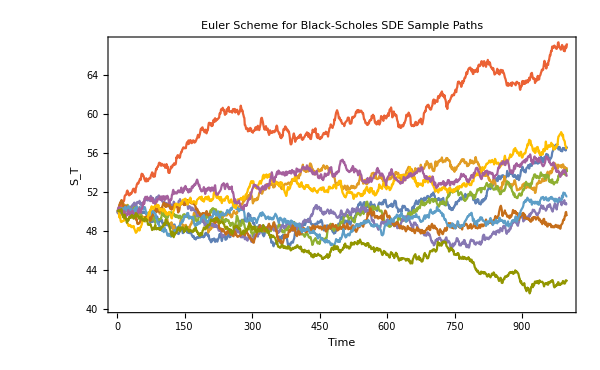

```mathematica
ListLinePlot[basicEulerBS[50, 0.06, 0.1,10],
PlotLabel->Style["Euler Scheme for Black-Scholes SDE Sample Paths",Black],
Frame->True,
FrameLabel->{"Time","S_T"},
FrameStyle->Black,
ImageSize->{600,350}]
```

```mathematica
EulerBS[S0_, r_, σ_, T_]:= Module[{proc, dt,S,W},
								dt =T/1000;
								proc= ItoProcess[ⅆS[t] == r(S[t])ⅆt + σ(S[t])ⅆW[t], S[t], {S,S0}, t, Distributed[W, WienerProcess[]]];
								Return[RandomFunction[proc,{0.,T,dt}, 10, Method->"EulerMaruyama"]]
								]
```

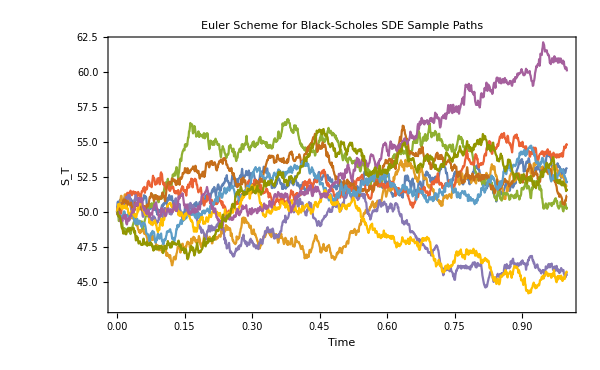

```mathematica
ListLinePlot[EulerBS[50, 0.06, 0.1, 1],
PlotLabel->Style["Euler Scheme for Black-Scholes SDE Sample Paths",Black],
Frame->True,
FrameLabel->{"Time","S_T"},
FrameStyle->Black,
ImageSize->{600,350}]
```

We compare the run time for both methods above

```mathematica
StringForm["Run time for the basic Euler Method: " <> ToString[Timing[basicEulerBS[50, 0.06, 0.1,10]][[1]]]]
StringForm["Run time for for Euler method using Mathematica's ItoProcess and RandomFunction: " <> ToString[Timing[EulerBS[50, 0.06, 0.1, 1]][[1]]]]
```

Run time for the basic Euler Method: 0.203125

Run time for for Euler method using Mathematica's ItoProcess and RandomFunction: 0.03125

Monte Carlo estimations are computationally expensive and hence huge consideration is given to the performance of a Monte Carlo algorithm. As seen from the result above,  the second approach is simpler and approximately 50% more faster. However for Monte Carlo estimation the second method will not be used as we would need to generate large sample path (> 1000), since the ItoProcess and RandomFunction approach gives all data point from t=0 to t=1, this will reduce performance drastically as the number of sample paths increase. For plotting sample paths the second approach will be used.

### Euler-Maruyama Discretization of Heston Model

The Heston model is described by the bivariate stochastic process for the stock price S_t and it’s variance v_t

dS_t = rS_t dt+√v_t S_t dW_(1,t)
dv_t= κ(θ -v_t)+σ √v_t dW_(2, t)
where E[dW_(1,t)dW_(2,t)] = ρdt

The SDE for v_t in equation 14 in integral form is

v_(t+dt) = v_t+(∫_t)^(t+dt)κ(θ - v_u)du+(∫_t)^(t+dt)σ √v_u dW_(2,u)

The Euler discretization approximation for the above equation is

v_(t+dt) = v_t+κ(θ - v_u)dt + σ √(v_t dt)Z_v

SDE for S_tin equation 14  can be written in integral form as;

S_(t+dt) = S_t+r(∫_t)^(t+dt)S_u du+(∫_t)^(t+dt)σ √v_u S_u dW_u

The Euler discretization approximation for the above equation is

S_(t+dt) = S_t+rS_t dt+√(v_t dt)S_t Z_s

To simulate path from the Heston model using equation 14 using the Euler-Maruyama Scheme;

```mathematica
EulerHeston [r_, σ_, κ_, θ_, ρ_,v0_,S0_] := Module[{S,v,paths,proc, corW, Ws, Wv},
												corW = ItoProcess[{{0,0},IdentityMatrix[2]},{{w1,w2},{0,0}},t,{{1,ρ},{ρ,1}}]; (*2-dimension correlated Wiener process*)
												proc = ItoProcess[{ⅆS[t] == r S[t]ⅆt+√v[t] S[t]ⅆWs[t],
																ⅆv[t] == κ(θ-v[t])ⅆt+σ √v[t] ⅆWv[t]},
																	{S[t],v[t]},{{S,v},{S0,v0}},t,Distributed[{Ws,Wv},corW ]];
												paths = RandomFunction[proc, {0,1,1/1000},10, Method -> "EulerMaruyama"];
												{paths["PathComponent",1], paths["PathComponent",2]}
											]
```

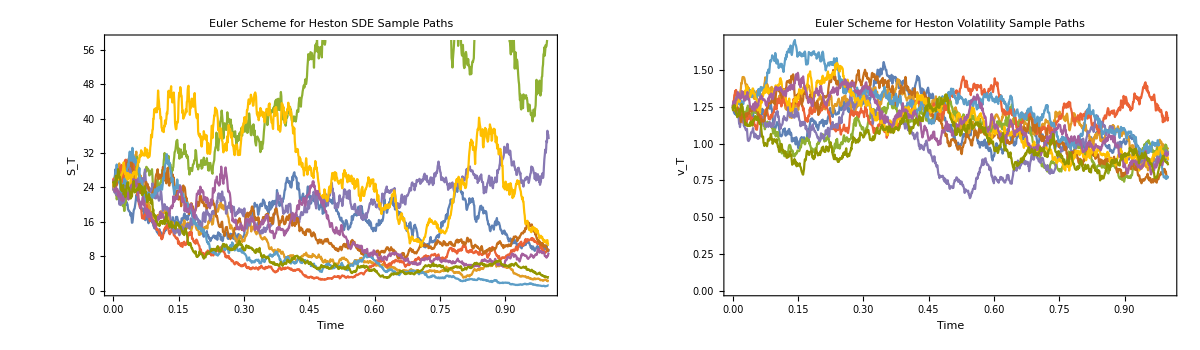

```mathematica
GraphicsRow[{ListLinePlot[EulerHeston [0,0.5,2,1,-0.33,1.25,25][[1]],
PlotLabel->Style["Euler Scheme for Heston SDE Sample Paths",Black],
Frame->True,
FrameLabel->{"Time","S_T"},
FrameStyle->Black,
ImageSize->{600,350}], ListLinePlot[EulerHeston [0,0.5,2,1,-0.33,1.25,25][[2]],
PlotLabel->Style["Euler Scheme for Heston Volatility Sample Paths",Black],
Frame->True,
FrameLabel->{"Time","v_T"},
FrameStyle->Black,
ImageSize->{600,350}]},ImageSize->{1200,350}]
```

## Milstein Scheme

The Milstein scheme works for stochastic differential equations for which the coefficients μ(X_t) and σ(X_t)  depends only on X, and do not depend on t directly. Hence we assume that the stock price S_t is driven by the SDE

dS_t=μ(S_t)dt+σ(S_t)dW_t
= μdt + σ_t dW_t

The above equation written in integral form is

S_(t+dt)=S_t+(∫_t)^(t+dt)μ_s ds+(∫_t)^(t+dt)σ_s dW_s

Without going into the details of how equation 20 is discretized using Milstein scheme, the general form of Milstein discretization is

S_(t+dt)=S_t +μ_t dt+σ √dt Z+1/2 σ'_t σ_t dt(Z^2-1)

### Milstein Discretization of Black-Scholes Model

In the Black Scholes model equation (10) we have μ(S_t) = rS_t and σ(S_t) = σS_t, applying the Milstein scheme (equation 21) we have

S_(t+dt)=S_t +rS_t dt+σS_t √dt Z+1/2 σ^2 dt(Z^2-1)

The log form of the above equation will reduce to the Euler Maruyama discretization

```mathematica
basicMilsteinBS[S0_, r_, σ_] := Module[{path,dt},
									With[{t = 1},dt = t/1000];
								path = {p1, p2, p3, p4, p5, p6, p7,p8,p9,p10};
								Table[path[[i]]= Range[1000];
										path[[i]][[1]] = S0;
										Table[path[[i]][[j]]= path[[i]][[j-1]]+r path[[i]][[j-1]] dt+σ path[[i]][[j-1]] √dt RandomVariate[NormalDistribution[0,1]]+1/2 σ^2 dt (( RandomVariate[NormalDistribution[0,1]])^2-1),{j,2,1000}]; ,{i, 1, 10}];
								Return[path]
]
```

```mathematica
MilsteinBS[S0_, r_, σ_, T_]:= Module[{S,proc, dt,W},
								dt =T/1000;
								proc= ItoProcess[ⅆS[t] == r(S[t])ⅆt + σ(S[t])ⅆW[t], S[t], {S,S0}, t, Distributed[W, WienerProcess[]]];
								Return[RandomFunction[proc,{0.,T,dt}, 10, Method->"Milstein"]]
								]
```

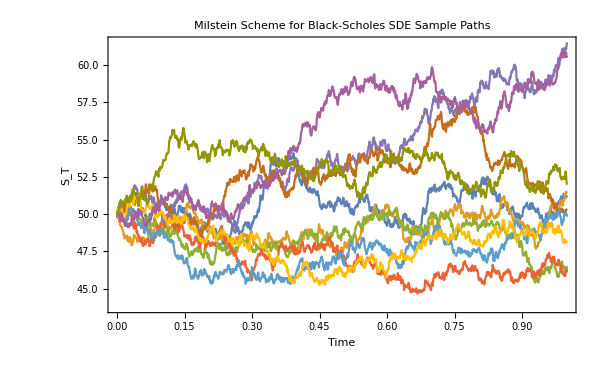

```mathematica
ListLinePlot[MilsteinBS[50, 0.06, 0.1,1],
PlotLabel->Style["Milstein Scheme for Black-Scholes SDE Sample Paths",Black],
Frame->True,
FrameLabel->{"Time","S_T"},
FrameStyle->Black,
ImageSize->{600,350}]
```

### Milstein Discretization of Heston Model

The Milstein model given in equation 14

dS_t = rS_t dt+√v_t S_t dW_(1,t)
dv_t= κ(θ -v_t)+σ √v_t dW_(2, t)
where E[dW_(1,t)dW_(2,t)] = ρdt

The Milstein discretization for equation 14 for v_t with the coefficients of the variance process μ(v_t) = κ(θ-v_t) and σ(v_t) = σ √v_t

v_(t+dt)=v_t+κ(θ-v_t)dt+σ √(v_t dt)Z_v+1/4 σ^2 dt(Z_v^2-1)
can also be written as
v_(t+dt)=(√v_t+1/2 σ^2 √dt Z_v)^2+κ(θ-v_t)dt-1/4 σ^2 dt

Milstein discretization for equation 14 for S_t with the coefficients of the stock price μ(S_t) = rS_t and σ(S_t) = √v_t S_t

S_(t+dt) = S_t+rS_t dt+√(v_t dt)S_t Z_s+1/4 S_t^2 dt(Z_s^2-1)

To simulate paths from the Heston model using Milstein scheme;

```mathematica
MilsteinHeston [r_, σ_, κ_, θ_, ρ_,v0_,S0_] := Module[{S,v,Wv,Ws,w1,w2,paths,proc, corW},
												corW = ItoProcess[{{0,0},IdentityMatrix[2]},{{w1,w2},{0,0}},t,{{1,ρ},{ρ,1}}]; (*2-dimension correlated Wiener process*)
												proc = ItoProcess[{ⅆS[t] == r S[t]ⅆt+√v[t] S[t]ⅆWs[t],
																ⅆv[t] == κ(θ-v[t])ⅆt+σ √v[t] ⅆWv[t]},
																	{S[t],v[t]},{{S,v},{S0,v0}},t,Distributed[{Ws,Wv},corW ]];
												paths = RandomFunction[proc, {0,1,1/1000},10, Method -> "Milstein"];
												{paths["PathComponent",1], paths["PathComponent",2]}
											]
```

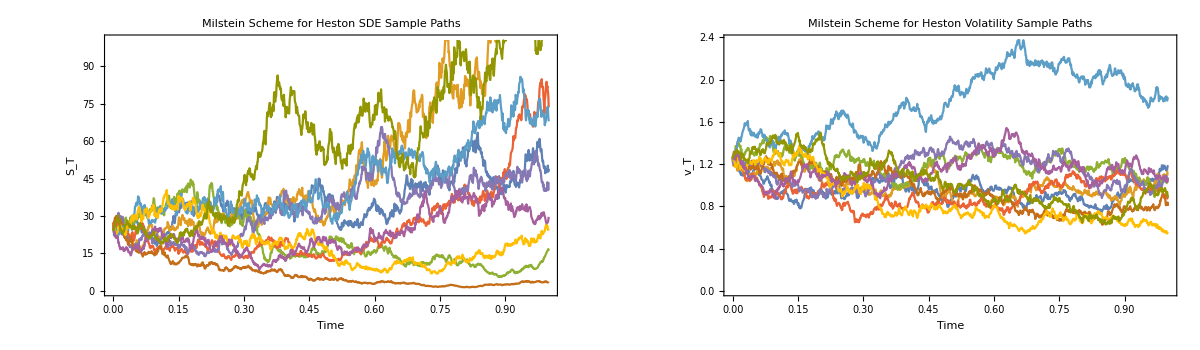

```mathematica
GraphicsRow[{ListLinePlot[MilsteinHeston [0,0.5,2,1,-0.33,1.25,25][[1]],
PlotLabel->Style["Milstein Scheme for Heston SDE Sample Paths",Black],
Frame->True,
FrameLabel->{"Time","S_T"},
FrameStyle->White,
ImageSize->{600,350}], ListLinePlot[MilsteinHeston [0,0.5,2,1,-0.33,1.25,25][[2]],
PlotLabel->Style["Milstein Scheme for Heston Volatility Sample Paths",Black],
Frame->True,
FrameLabel->{"Time","v_T"},
FrameStyle->Black,
ImageSize->{600,350}]},ImageSize->{1200,350}]
```

## Monte Carlo Estimation of S_t and European Call Option (Using Black Scholes Model)

For the final time expected value of the solution to equation 10 and equation 14, E[S(T)] using Monte Carlo with any of the following discretization methods (EulerMaruyama, KloedenPlatenSchurz, Milstein,  StochasticRungeKutta, StochasticRungeKuttaScalarNoise). 
Let S_N^s denote the discretized final time approximation along the sth path. Using Monte Carlo samples we may form the sample average

(Ŝ)_T=1/M∑_(s=1)^M S_N^s

```mathematica
MCBlackScholes[S0_, r_, σ_, T_, p_,discretization_,n_]:=Module[{S,dt,W, methods, paths, assoc, proc},
															methods={"EulerMaruyama", "KloedenPlatenSchurz","Milstein", "StochasticRungeKutta","StochasticRungeKuttaScalarNoise"};
															If[!StringQ[discretization]||!MemberQ[methods, discretization], Return[StringForm["Invalid discretization method specified"]]];
															dt =T/n;
															proc=ItoProcess[ⅆS[t] == r(S[t])ⅆt + σ(S[t])ⅆW[t], S[t], {S,S0}, t, Distributed[W, WienerProcess[]]];
															paths= RandomFunction[proc,{0,T,dt}, p, Method->discretization];
															assoc= Association[{"Data"-> paths,"Estimate"-> Mean[paths[[2,1]][[All,n+1]]]}];
															Return[assoc]
														]
```

Monte Carlo estimation of S_T using the Black-Scholes model - Euler-Maruyama Discretization with 100 sample path (M = 100)

```mathematica
StBS =MCBlackScholes[50, 0.12, 0.1, 1,100,"EulerMaruyama",1000]["Estimate"]
```

56.546

```mathematica
MCHeston [r_, σ_, κ_, θ_, ρ_,v0_,S0_,discretization_,n_,P_] := Module[{S,paths,proc, corW, methods, temp, assoc,T,dt},
												methods={"EulerMaruyama", "KloedenPlatenSchurz","Milstein", "StochasticRungeKutta","StochasticRungeKuttaScalarNoise"};
												If[!StringQ[discretization]||!MemberQ[methods, discretization], Return[StringForm["Invalid discretization method specified"]]];
												T = 1;dt = T/n;
												corW = ItoProcess[{{0,0},IdentityMatrix[2]},{{w1,w2},{0,0}},t,{{1,ρ},{ρ,1}}]; (*2-dimension correlated Wiener process*)
												proc = ItoProcess[{ⅆS[t] == r S[t]ⅆt+√v[t] S[t]ⅆSubscript[W, s][t],
																ⅆv[t] == κ(θ-v[t])ⅆt+σ √v[t] ⅆSubscript[W, v][t]},
																	{S[t],v[t]},{{S,v},{S0,v0}},t,Distributed[{Subscript[W, s],Subscript[W, v]},corW ]];
												paths = RandomFunction[proc, {0,T,dt},P, Method -> discretization];
												assoc = Association[{"Data"-> paths["PathComponent",1],"Volatility"-> paths["PathComponent",2],"Estimate"-> Mean[paths["PathComponent",1][[2,1]][[All,n+1]]]}];
												Return[assoc]
											]
```

Monte Carlo estimation of S_T using the Heston model - Euler-Maruyama Discretization with 100 sample path (M = 100)

```mathematica
StH = MCHeston[0,0.5,2,1,-0.33,1.25,50,"EulerMaruyama",1000,100]["Estimate"]
```

51.1223

European Option:  A European option refers to contracts that give the investor the right to buy, or sell, and asset at a specific price(Strike Price (K)) on a certain date T. A European call option is a contract between two parties, a holder and a writer, whereby for a premium paid to the writer , the  holder acquires the right (but not obligated) to purchase the stock at a future data T (the expiration date) at a price K (the strike price) agreed upon in the contract. If the buyer elects to exercise the option on the expiration date, the writer is obligated to sell the underlying stock to the buyer at the price K. Thus the option has, associated with it a payoff function

f(S) = max(S-K,0)
Where S = S_T is the price of the underlying stock at the time T when the option expires

From the equation above if S_T> K, the holder can purchase at price K, stock with market value S_T and thereby make a profit equal to S_T - K, not counting the option premium (C). If S_T < 0, then it is not in the holders interest to buy.
At time T we know the profit and also the value of Stock price at time T. How do we calculate it for time t = 0 and the premium C at time t = 0. The no arbitrage assumptions of Black-Scholes theory imply that the present value of the European call option is

C(S_0,T) = e^-rT E(max(S_T-k,0))
Where S_T satisfies the SDE in equation 10

The expectation of equation 26 can be approximated using Monte Carlo estimation and result can be compared with the exact solution from the Black-Scholes formula.

C(S,T) = SN(d_1)-Kⅇ^-rT N(d_2)
where
d_1 = (log(S/K)+(r+1/2 σ^2)T)/(σ √T),d_2=(log(X/K)+(r-1/2 σ^2)T)/(σ √T), N = cumulative Standard Normal Distribution

The basicEulerBS function will be modified to obtain Monte Carlo Estimate of call option. We will not use the Ito Process and random function for simulation as we need to simulate large number of paths and wouldn’t have any need for all data-points from t=0 to t=1, just the value at T=1, which can be gotten directly for both Euler-Maruyama and Milstein Scheme using equation 13 and 22 respectively.

```mathematica
MCOPTBS[S0_, r_, σ_, dt_,discretization_,n_,SK_]:=Module[{ST, methods,payoff,Z, CI,est},
													methods={"EulerMaruyama","Milstein"};
													If[!StringQ[discretization]||!MemberQ[methods, discretization], Return[StringForm["Invalid discretization method specified"]],
														payoff= Range[n];
														Z = NormalDistribution[0,1];
														If[discretization == "EulerMaruyama",
															For[i = 1,i ≤ n, i++,ST= S0 Exp[(r-σ^2/2)dt+σ √dt RandomVariate[Z]];
																payoff[[i]] =ⅇ^(-r dt)* Max[ST-SK,0];];
															CI = 1.96*StandardDeviation[payoff]/(√n);(*95% Confidence Interval*)
															est = Mean[payoff];
															Return[{est,CI}], 
															(*Milstien*)
															For[i = 1,i ≤ n, i++,ST=  S0+r S0 dt+σ S0 √dt RandomVariate[Z]+1/2 σ^2 dt (( RandomVariate[Z])^2-1); 
																payoff[[i]] =ⅇ^(-r dt)* Max[ST-SK,0];];
															CI = 1.96*StandardDeviation[payoff]/(√n);(*95% Confidence Interval*)
															est = Mean[payoff];
															Return[{est,CI}]  
														]
													]
													]
```

Function to calculate equation 27 at various Time and S_T returns exact Cs and plot

```mathematica
ExactBS[T_, S_]:= With[{r =0.06,σ = 0.2, SK = 45},Module[{assoc,c, d1, d2,plot},
					d1 = Table[(Log[S[[i]]/SK]+(r+σ^2/2)*T[[i]])/(σ*√T[[i]]),{i,1, Length[S]}];
					d2 = Table[d1[[i]] - (σ*√T[[i]]),{i, 1, Length[S]}];
					c = Table[S[[i]]*CDF[NormalDistribution[0,1],d1[[i]]]-SK* ⅇ^(-r (T[[i]]))*CDF[NormalDistribution[0,1],d2[[i]]] ,{i,1, Length[S]}];
					plot = ListPlot3D[{S,c,T}, ColorFunction->"Rainbow",
					PlotLabel->Style["European Call Option: Exact Solution",Black]];
					assoc = Association[{"C" -> c,"Plot"-> plot}];
					Return[assoc]
				]]
```

We compute Monte Carlo Estimate and exact solution for European call option using the follow parameters;
i. T = {0.1,0.3,0.5,0.7,0.9}
ii. S_T= {40,42,44,46,48}
iii. Strike price K = 45
iv. Volatility σ = 0.2
v. Risk free rate r = 0.06
vi. initial Stock price S0 = 40
vii. paths (m = 1,000, 10,000, 100,000) we will compare  estimates at different m

```mathematica
S = Table[i,{i,40,49,2}];
T = Range[0.1,1,0.2];
```

```mathematica
exactFullR = ExactBS[T,S];
```

```mathematica
exactFullR["C"]
```

{0.0414183,0.984034,2.63954,4.61162,6.75251}

```mathematica
exactFullR["Plot"]
```

-Graphics3D-

```mathematica
Clear[res];
res = Table[Table[MCOPTBS[S[[i]], 0.06, 0.2, T[[i]],"Milstein",j,45],{i,1,5}],{j,{1000,10000,100000}}];
Grid[Transpose[res[[All,All,1]]], Frame->All]
Grid[Transpose[Table[Abs[res[[i,All,1]]-exactFullR["C"]],{i,1,3}]], Frame->All]
```

0.021666 | 0.0263692 | 0.0279251
0.933248 | 0.895653 | 0.911175
2.55746 | 2.57446 | 2.56836
4.81857 | 4.65088 | 4.56084
7.08235 | 6.69652 | 6.69685

0.0197523 | 0.0150491 | 0.0134933
0.0507866 | 0.0883815 | 0.072859
0.0820742 | 0.0650752 | 0.0711772
0.206952 | 0.0392603 | 0.0507786
0.329834 | 0.0559948 | 0.0556604

Monte Carlo Estimate (via Milstein) vrs Exact Solution 				Absolute difference between Exact and MC Estimate
S_T/T | m=1000 | m=10000 | m=100000 | Exact
40/0.1 | 0.021666 | 0.0263692 | 0.0279251 | 0.0414183
42/0.3 | 0.933248 | 0.895653 | 0.911175 | 0.984034
44/0.5 | 2.55746 | 2.57446 | 2.56836 | 2.63954
46/0.7 | 4.81857 | 4.65088 | 4.56084 | 4.61162
48/0.9 | 7.08235 | 6.69652 | 6.69685 | 6.75251	S_T/T | m=1000 | m=10000 | m=100000
40/0.1 | 0.0197523 | 0.0150491 | 0.0134933
42/0.3 | 0.0507866 | 0.0883815 | 0.072859
44/0.5 | 0.0820742 | 0.0650752 | 0.0711772
46/0.7 | 0.206952 | 0.0392603 | 0.0507786
48/0.9 | 0.329834 | 0.0559948 | 0.0556604

```mathematica
Clear[p1,p2,p3];
p1 = ListLinePlot[{res[[1,All,1]],exactFullR["C"]},PlotLabel->Style["Milstein vrs Exact m = 10^3)]",Black], PlotLegends->{"Milstein","Exact"}];
p2= ListLinePlot[{res[[2,All,1]],exactFullR["C"]},PlotLabel->Style["Milstein vrs Exact m = 10^4)]",Black], PlotLegends->{"Milstein","Exact"}];
p3 = ListLinePlot[{res[[3,All,1]],exactFullR["C"]},PlotLabel->Style["Milstein vrs Exact m = 10^5)]",Black], PlotLegends->{"Milstein","Exact"}];
GraphicsRow[{p1,p2,p3},ImageSize->{1200,300},Spacings->20]
```

-Graphics-

```mathematica
ListPlot3D[{S,res[[3,All,1]],T}, ColorFunction->"Rainbow",
					PlotLabel->Style["European Call Option: Monte Carlo Estimates (Via Milstein, m = 10^5)]",Black],
					ImageSize->{600,350}]
```

-Graphics3D-

```mathematica
Clear[res];
res = Table[Table[MCOPTBS[S[[i]], 0.06, 0.2, T[[i]],"EulerMaruyama",j,45],{i,1,5}],{j,{1000,10000,100000}}];
Grid[Transpose[res[[All,All,1]]], Frame->All]
Grid[Transpose[Table[Abs[res[[i,All,1]]-exactFullR["C"]],{i,1,3}]], Frame->All]
```

0.0430173 | 0.0378926 | 0.0398831
0.896041 | 0.98475 | 0.982788
2.6019 | 2.58874 | 2.63305
4.60567 | 4.57612 | 4.60181
6.41442 | 6.81809 | 6.74233

0.00159894 | 0.00352576 | 0.00153519
0.0879928 | 0.000716298 | 0.00124605
0.0376396 | 0.050791 | 0.00648518
0.00594927 | 0.035504 | 0.00981458
0.338093 | 0.0655748 | 0.0101845

Monte Carlo Estimate (via EM) vrs Exact Solution 				Absolute difference between Exact and MC Estimate
S_T/T | m=1000 | m=10000 | m=100000 | Exact
40/0.1 | 0.0430173 | 0.0378926 | 0.0398831 | 0.0414183
42/0.3 | 0.896041 | 0.98475 | 0.982788 | 0.984034
44/0.5 | 2.6019 | 2.58874 | 2.63305 | 2.63954
46/0.7 | 4.60567 | 4.57612 | 4.60181 | 4.61162
48/0.9 | 6.41442 | 6.81809 | 6.74233 | 6.75251	S_T/T | m=1000 | m=10000 | m=100000
40/0.1 | 0.00159894 | 0.00352576 | 0.00153519
42/0.3 | 0.0879928 | 0.000716298 | 0.00124605
44/0.5 | 0.0376396 | 0.050791 | 0.00648518
46/0.7 | 0.00594927 | 0.035504 | 0.00981458
48/0.9 | 0.338093 | 0.0655748 | 0.0101845
Overall there is more decrease as m increases.

```mathematica
Clear[p1,p2,p3];
p1 = ListLinePlot[{res[[1,All,1]],exactFullR["C"]},PlotLabel->Style["EM vrs Exact m = 10^3)]",Black], PlotLegends->{"EM","Exact"}];
p2= ListLinePlot[{res[[2,All,1]],exactFullR["C"]},PlotLabel->Style["EM vrs Exact m = 10^4)]",Black], PlotLegends->{"EM","Exact"}];
p3 = ListLinePlot[{res[[3,All,1]],exactFullR["C"]},PlotLabel->Style["EM vrs Exact m = 10^5)]",Black], PlotLegends->{"EM","Exact"}];
GraphicsRow[{p1,p2,p3},ImageSize->{1200,300},Spacings->20]
```

-Graphics-

```mathematica
ListPlot3D[{S,res[[3,All,1]],T}, ColorFunction->"Rainbow",
					PlotLabel->Style["European Call Option: Monte Carlo Estimates (Via EM, m = 10^5)]",Black],
					ImageSize->{600,350}]
```

-Graphics3D-

### 95% Confidence Interval (Margin of Error of Estimate)

```mathematica
Clear[res];
res = {Table[MCOPTBS[S[[i]], 0.06, 0.2, T[[i]],"EulerMaruyama",100000,45],{i,1,5}],Table[MCOPTBS[S[[i]], 0.06, 0.2, T[[i]],"Milstein",100000,45],{i,1,5}]};
Grid[Transpose[res[[All,All,1]]], Frame->All]
Grid[Transpose[res[[All,All,2]]], Frame->All]
```

0.0420505 | 0.0300647
0.981798 | 0.913225
2.64926 | 2.55625
4.61143 | 4.55118
6.78714 | 6.70308

0.001822 | 0.00141819
0.0132637 | 0.0116914
0.0252876 | 0.0223967
0.0364791 | 0.0324081
0.0472403 | 0.0414128

S_T/T | EM | CI for EM | Milstein | CI for Milstein | Exact
40/0.1 | 0.0418496 | 0.00184117 | 0.0297193 | 0.00143097 | 0.0414183
42/0.3 | 0.995365 | 0.0133576 | 0.903292 | 0.0115999 | 0.984034
44/0.5 | 2.63152 | 0.0251829 | 2.54565 | 0.0223456 | 2.63954
46/0.7 | 4.61207 | 0.0363936 | 4.55336 | 0.0323127 | 4.61162
48/0.9 | 6.75458 | 0.0468644 | 6.70307 | 0.0416281 | 6.75251
Overall we see that the Euler-Maruyama discretization do better than the Milstein Scheme. For the EM scheme the exact values fall with the confidence interval, this is not exactly the same for the Milstein scheme. From the table above the first row (S_t = 40, T = 0.1) the Exact value is outside the confidence interval band for MC estimate of Milstein Scheme. (i.e 0.0414183 > 0.029713 ±0.00143097)

### Variance Reduction for Monte Carlo Estimate

There are various variance reduction methods for Monte Carlo estimates. In this report , Antithetic variates will be used to reduce the variance of our estimate.
The basic idea of antithetic variates is simple. We obtain a variate Z^* which has the same distribution as Z, in particular, the same mean and variance but is negatively correlated with Z.

θ̂ = 1/2(Z+Z^*)
is an unbiased estimator of θ
Var(θ̂) = 1/4(Var(Z)+Var(Z^*)+ 2 Cov(Z,Z^*))
=1/2 Var(Z){1+corr(Z,Z^*)}.

If the correlation between Z and Z^* is negative, then this yields a reduction in variance.
Since we generated standard normal distribution for our estimate, we can use -Z as our anitvariate since it’s symmetric. The MCOPTBS function is modified to include the antivariate.

```mathematica
VRMCOPTBS[S0_, r_, σ_, dt_,discretization_,n_,SK_]:=Module[{ST, ST2, methods, est,prices,payoff,Z,CI},
													methods={"EulerMaruyama","Milstein"};
													If[!StringQ[discretization]||!MemberQ[methods, discretization], Return[StringForm["Invalid discretization method specified"]],
														prices = payoff= Range[n];
														Z = NormalDistribution[0,1];
														If[discretization == "EulerMaruyama",
															For[i = 1,i ≤ n, i++,ST= S0 Exp[(r-σ^2/2)dt+σ √dt RandomVariate[Z]];ST2= S0 Exp[(r-σ^2/2)dt+σ √dt (RandomVariate[Z]*-1)];
																payoff[[i]] =ⅇ^(-r dt)* (Max[ST-SK,0]+Max[ST2-SK,0])/2;];
															CI = 1.96*StandardDeviation[payoff]/(√n);(*95% Confidence Interval*)
															est = Mean[payoff];
															Return[{est,CI}],   
															(*Milstien*)
															For[i = 1,i ≤ n, i++,ST=  S0+r S0 dt+σ S0 √dt RandomVariate[Z]+1/2 σ^2 dt (( RandomVariate[Z])^2-1);
																ST2=  S0+r S0 dt+σ S0 √dt (RandomVariate[Z]*-1)+1/2 σ^2 dt (( ((RandomVariate[Z])*-1))^2-1);
																payoff[[i]] =ⅇ^(-r dt)* (Max[ST-SK,0]+Max[ST2-SK,0])/2;];
															CI = 1.96*StandardDeviation[payoff]/(√n);(*95% Confidence Interval*)
															est = Mean[payoff];
															Return[{est,CI}]  
														]
													]
													]
```

```mathematica
Clear[res];
res = {Table[VRMCOPTBS[S[[i]], 0.06, 0.2, T[[i]],"EulerMaruyama",100000,45],{i,1,5}],Table[VRMCOPTBS[S[[i]], 0.06, 0.2, T[[i]],"Milstein",100000,45],{i,1,5}]};
Grid[Transpose[res[[All,All,1]]], Frame->All]
```

0.0406217 | 0.0300653
0.984358 | 0.910134
2.63729 | 2.56716
4.59571 | 4.55324
6.74239 | 6.72777

Monte Carlo Estimate with Antithetic Variance Reduction 
S_T/T | EM | Milstein | Exact | Abs(EM-Exact) | Abs(Milstein-Exact)
40/0.1 | 0.0406217 | 0.0300653 | 0.0414183 | 0.000796605 | 0.011353
42/0.3 | 0.984358 | 0.910134 | 0.984034 | 0.000323846 | 0.0739005
44/0.5 | 2.63729 | 2.56716 | 2.63954 | 0.00224523 | 0.0723711
46/0.7 | 4.59571 | 4.55324 | 4.61162 | 0.0159098 | 0.0583848
48/0.9 | 6.74239 | 6.72777 | 6.75251 | 0.0101229 | 0.0247485

```mathematica
Clear[res];
res = {Table[MCOPTBS[S[[i]], 0.06, 0.2, T[[i]],"EulerMaruyama",100000,45],{i,1,5}],Table[MCOPTBS[S[[i]], 0.06, 0.2, T[[i]],"Milstein",100000,45],{i,1,5}]};
Grid[Transpose[res[[All,All,1]]], Frame->All]
```

0.0415722 | 0.0278534
0.996475 | 0.909235
2.6453 | 2.58047
4.60429 | 4.55407
6.73308 | 6.74439

Ordinary Monte Carlo Estimates
S_T/T | EM | Milstein | Exact | Abs(EM-Exact) | Abs(Milstein-Exact)
40/0.1 | 0.0415722 | 0.0278534 | 0.0414183 | 0.000153831 | 0.0135649
42/0.3 | 0.996475 | 0.909235 | 0.984034 | 0.0124406 | 0.0747993
44/0.5 | 2.6453 | 2.58047 | 2.63954 | 0.00575986 | 0.0590693
46/0.7 | 4.60429 | 4.55407 | 4.61162 | 0.00733335 | 0.0575497
48/0.9 | 6.73308 | 6.74439 | 6.75251 | 0.0194366 | 0.00812521
We observe that there is slight improvement in the estimates using variance reduction.

## Conclusion

In this report we looked at Monte Carlo estimation of solutions to Stochastic Differential Equation, using two popular discretization schemes, The Euler-Maruyama Scheme and the Milstein Scheme. The schemes where applied to the Black-Scholes model and the Heston model both of which follow the geometric Brownian motion. Mathematica’s ItoProcess and RandomFunction were used to show sample paths while function was written to compute Monte Carlo estimates, this was to improve performance as the RandomFunction saves all data points. The Black scholes solution to European call option was estimated and result compared with the exact solution, we saw that the difference between the Monte Carlo estimate and the exact result reduces as the number of samples increases. We also observed that the Euler Maruyama Scheme performed better than the Milstein scheme. To improve accuracy variance reduction was used (Antithetic variate) and there was slight improvement in the estimates. 

One of the main objective of this report was to explore Mathematica, having done this little and seen how powerful the program is, I am certain there is so much more to learn and uncover. Some follow-up of this report may include Monte Carlo estimation of Stochastic Differential Equation parameters such as the Drift and Diffusion terms. etc., Monte Carlo Estimation of other SDEs, Bayesian Inference with MCMC for discretization scheme selection, etc.